Create animation analogous to https://conwaylife.com/wiki/R-pentomino
Cut off gliders
Make the length 1103 case; possibly minimize cuboids

```mathematica
ArrayPlot[ArrayPad[#,2],Mesh->True,MeshStyle->Opacity[.2]]&/@CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{30, {-20, 20}, {-18, 20}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ArrayPad[#,2],Mesh->True,MeshStyle->Opacity[.2]]&/@CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{30, {-20, 20}, {-18, 20}}]
```

```mathematica
Dimensions[{{1, 1, 1}, {1, 1, 1}}]
```

{2,3}

```mathematica
CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, 1]
```

{{{0,1,1},{1,1,0},{0,1,0}},{{1,1,1},{1,0,0},{1,1,0}}}

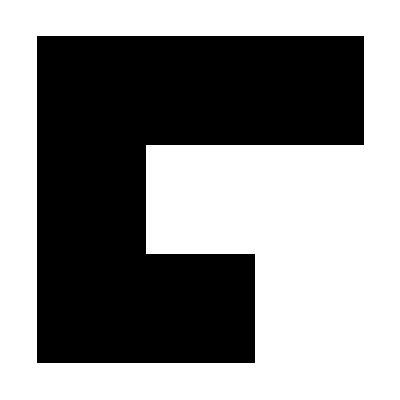

```mathematica
ArrayPlot[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{1}}}]]
```

```mathematica
{maxy, maxx}  = {5, 5};
```

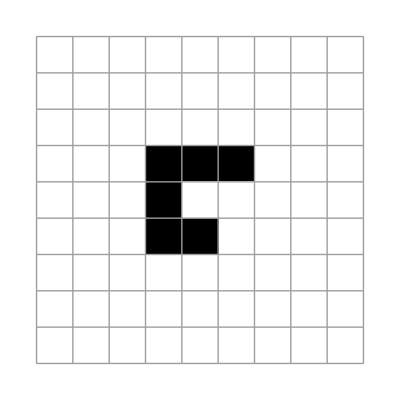

```mathematica
ArrayPlot[ArrayPad[#, {Floor[maxx - Length[#[[1]]] / 2], Floor[maxy - Length[#] / 2]}]&[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{1}}}]], Mesh->True]
```

```mathematica
padx
```

18

```mathematica
maxx -
```

9

```mathematica
maxx
```

9

```mathematica
padx =
```

```mathematica
maxy
```

9

```mathematica
padx
```

6

```mathematica
{maxx, maxy}  = {9, 9};
{padx, pady} = {6, 6};
Table[
With[{ca = CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{i}}}]},
(*{maxx, maxy}  = {Max[maxx,Length[ca[[1]]]], Max[maxy, Length[ca]]};*)
padx = padx + (padx - (maxx  - Length[ca[[1]]]));
pady= pady  + (pady - (maxy  - Length[ca]));
Echo[{padx, pady}];
ArrayPlot[ArrayPad[ca, {Floor[padx / 2], Floor[pady / 2]}], Mesh->True,MeshStyle->Opacity[.2], ImageSize->10{padx, pady}]], {i, 3}]
```

{6,6}

{7,7}

{9,9}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
maxx
```

6

```mathematica
{maxx, maxy}  = {9, 9};
{padx, pady} = {3, 3};
ListAnimate[
Table[
With[{ca = CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{i}}}]},
(*{maxx, maxy}  = {Max[maxx,Length[ca[[1]]]], Max[maxy, Length[ca]]};*)
maxx = maxx + Ramp[(2padx -  (maxx  - Length[ca[[1]]]))];
maxy= maxy  + Ramp[(2pady -(maxy  - Length[ca]))];
ArrayPlot[ArrayPad[ca, {3, 3}], Mesh->True,MeshStyle->Opacity[.2], ImageSize->{10maxx,10 maxy}(*Automatic*)]], {i, 30}]]
```

```mathematica
ArrayPlot[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{30}}, {-30, 45}, {-40, 100}}]]
```

-Graphics-

```mathematica
frames = 
Table[
ArrayPlot[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{i}}, {-25, 35}, {-45, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 500}];
```

```mathematica
ListAnimate[frames]
```

```mathematica
Export["anim2.mp4", frames]
```

anim2.mp4

Deal with step 0 etc.

What does this mean^

```mathematica
Ta
```